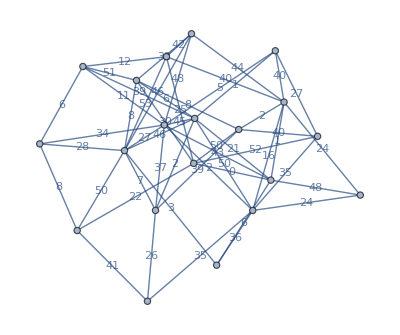

```mathematica
g=Graph[RandomGraph[{20,54}],EdgeCost->RandomInteger[{-54,54},54],EdgeWeight->RandomInteger[54,54],EdgeLabels->"EdgeWeight"]
```

```mathematica
FindMinimumCostFlow[g,1,3]
```

2

```mathematica
EvenMixedGraphAlgorithm[g_?MixedGraphQ]:=Block[{arcs,edges},arcs=EdgeList[g,_->_];edges=EdgeList[g,_<->_];]
```

```mathematica
EdgeList[g],RandomInteger[EdgeCount[g]]
```

{12<->16,7<->18,10<->14,7<->13,2<->14,19<->20,7<->16,1<->3,6<->18,6<->19}

```mathematica
?"*Replace*"
```

```mathematica
DirectedEdge[a<->b]
```

DirectedEdge[a<->b]

```mathematica
First[a<->b]
```

a

```mathematica
EdgeList[g]/.BlockRandom@RandomChoice[{a_<->b_:>a->b,a_<->b_:>a<->b}]
```

{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20}

```mathematica
MapAt[(First[#]->Last[#])&,EdgeList[g],RandomInteger[{1,54},4]]
```

MapAt::partw: Part {31,24,10,43} of {1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,«44»} does not exist.

MapAt[First[#1]->Last[#1]&,{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20},{31,24,10,43}]

```mathematica
MapAt[(First[#]->Last[#])&,{a<->b,b<->c,c<->d,d<->a},List/@BlockRandom[RandomInteger[{2,3},2]]]
```

{a<->b,b->c,c<->d,d<->a}

I was trying to create a replace edges in graph function but couldn’t figure it out. I was also trying to create a replace in a random place but couldn’t figure it out either.

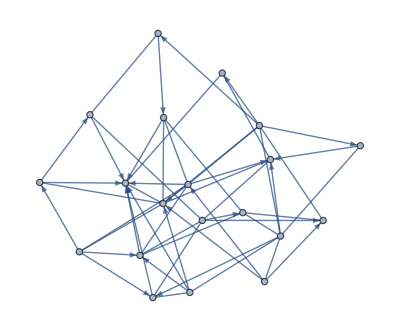

```mathematica
Graph@ReplaceAt[EdgeList[g],x_:>(First[x]->Last[x]),List/@RandomSample[Range@EdgeCount[g],27]]
```

```mathematica
specialembeddings=#<>"Embedding"&/@{"Bipartite","Circular","CircularMultipartite","DiscreteSpiral","Grid","Linear","Multipartite","Spiral","Star"};
```

```mathematica
structuredembeddings=#<>"Embedding"&/@{"Balloon","Radial","LayeredDigraph","Layered"};
```

```mathematica
optimizingembeddings=#<>"Embedding"&/@{"Gravity","HighDimensional","Planar","Spectral","Spherical","SpringElectrical","Spring","Tutte"};
```

```mathematica
graphembeddings=Flatten[{specialembeddings,structuredembeddings,optimizingembeddings}];
```

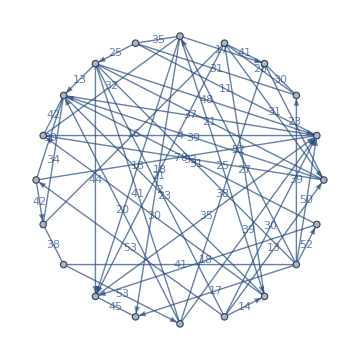
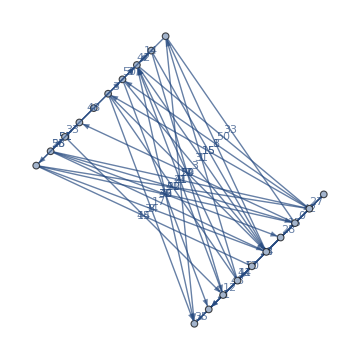
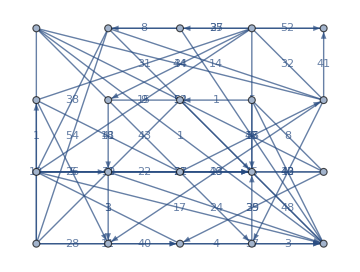
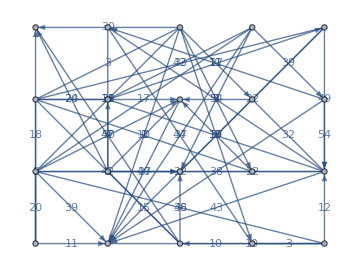
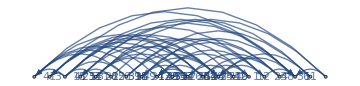
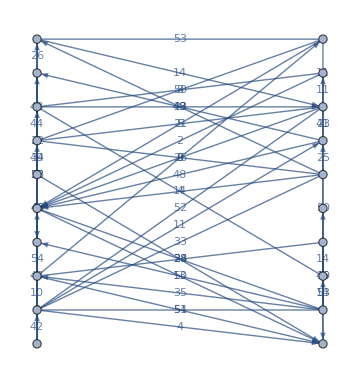
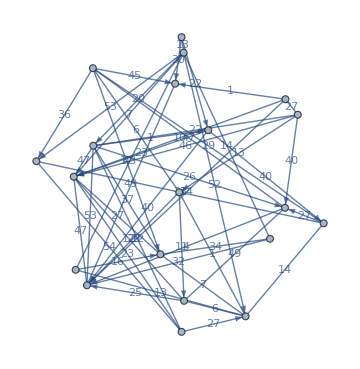
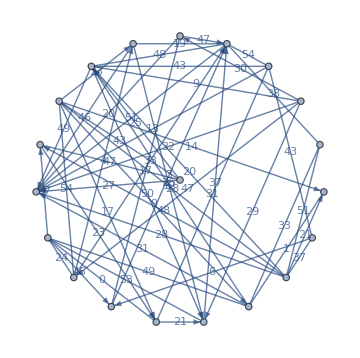

```mathematica
Graph[ReplaceAt[EdgeList[g],x_:>(First[x]->Last[x]),List/@RandomSample[Range@EdgeCount[g],27]],GraphLayout->#,EdgeWeight->RandomInteger[54,54],EdgeLabels->"EdgeWeight",ImageSize->Medium]&/@graphembeddings
```

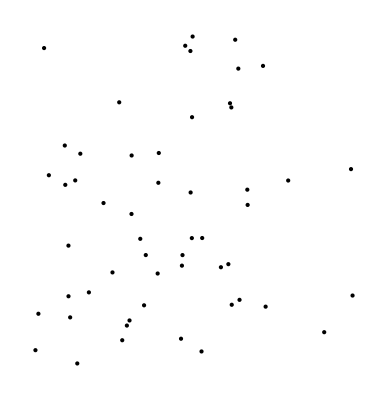

```mathematica
Graphics[Point@RandomPoint[Rectangle[{0,0},{20,20}],54]]
```

```mathematica
points=RandomPoint[Rectangle[{0,0},{20,20}],54]
```

{{17.6647,7.64676},{6.09097,10.1186},{8.6487,18.9197},{5.65971,18.641},{13.8322,12.2297},{15.8121,19.637},{2.30334,14.2538},{5.8598,6.36289},{8.45253,7.69844},{8.29064,12.03},{8.48785,7.3682},{14.0159,17.1232},{5.22403,9.6166},{15.0013,8.65067},{16.9324,7.79078},{3.5548,1.69398},{2.87122,0.155712},{0.688262,0.852099},{12.3955,17.4096},{0.203359,12.545},{3.86037,17.9369},{7.2969,13.3663},{17.5081,19.1008},{10.9098,11.3592},{17.0757,2.54315},{7.36498,16.6267},{17.8157,15.5448},{19.4799,9.98541},{17.8477,3.18781},{0.443176,16.7394},{5.74882,3.07568},{16.0237,18.1146},{10.5089,9.93099},{2.06086,4.41464},{19.4153,16.972},{11.474,16.4762},{12.0592,7.9111},{4.11464,4.09339},{13.2703,1.22539},{17.1468,17.0586},{19.799,12.9715},{10.5155,14.1105},{12.3381,11.699},{4.24721,8.52174},{4.45287,2.49065},{9.22285,7.15102},{7.08948,12.7369},{5.51228,0.474122},{17.6455,9.16901},{13.3714,19.0477},{8.9714,19.9487},{0.799153,16.0245},{3.2431,8.89804},{8.76347,6.59718}}

```mathematica
Nearest[Complement[points,{First[points]}],First[points],5]
```

{{16.9324,7.79078},{17.6455,9.16901},{15.0013,8.65067},{19.4799,9.98541},{17.8477,3.18781}}

```mathematica
EuclideanDistance[#,First[points]]&/@Nearest[Complement[points,{First[points]}],First[points],5]
```

{0.746399,1.52237,2.84634,2.96042,4.4627}

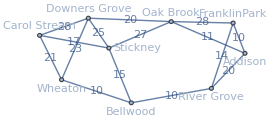
```mathematica
g=-Graphics-;
```

```mathematica
GeoGraphPlot[g]
```

-Graphics-

Compute and plot the most cost effective way of connecting all the cities:

```mathematica
fibernetwork=FindSpanningTree[g];
```

```mathematica
GeoGraphPlot[fibernetwork]
```

-Graphics-

```mathematica
GeoGraphValuePlot[{{Here,Interpreter["StreetAddress"]["1450 Huntington, West Virginia 25701"],GeoDistance[Here,Interpreter["StreetAddress"]["1450 Huntington, West Virginia 25701"]]}}]
```

-Graphics-

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"Dataset"]
```

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"TravelPath"]
```

GeoPath[GeoPosition[…],TravelPath]

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"ManeuverGrid"]
```

Continue onto Charleston Avenue | 0.302 km
Turn right onto 12th Street | 0.533 km
Turn left onto 8th Avenue | 0.615 km
Turn right onto 8th Street, WV 527 | 0.507 km
Arrive at destination |

```mathematica
GeoElevationData[Here,"Orthometric"]
```

174. m

```mathematica
GeoElevationData[GeoPosition[{38.4116094,-82.4345433}],"Orthometric"]
```

174. m

```mathematica
cities={Entity["City",{"Rome","Lazio","Italy"}]<->Entity["City",{"Milan","Lombardy","Italy"}],Entity["City",{"Milan","Lombardy","Italy"}]<->Entity["City",{"Paris","IleDeFrance","France"}],Entity["City",{"Milan","Lombardy","Italy"}]<->Entity["City",{"Frankfurt","Hesse","Germany"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"Frankfurt","Hesse","Germany"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"Madrid","Madrid","Spain"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Entity["City",{"Madrid","Madrid","Spain"}]<->Entity["City",{"Seville","Seville","Spain"}],Entity["City",{"Madrid","Madrid","Spain"}]<->Entity["City",{"Barcelona","Barcelona","Spain"}]};
```

```mathematica
GeoGraphValuePlot[Graph[cities, EdgeWeight->(QuantityMagnitude[TravelDistance[{First[#1],Last[#]},TravelMethod->"Walking"]]&/@cities)],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
nearbycities=GeoNearest["City",Here,20]
```

{Huntington,Chesapeake,Burlington,Proctorville,Barboursville,Ceredo,Lavalette,Pea Ridge,South Point,Kenova,Lesage,Catlettsburg,Ashland,Athalia,Wayne,Coal Grove,Salt Rock,Westwood,Ironton,Cannonsburg}

```mathematica
nearbyedges=UndirectedEdge@@@Transpose@{Most@nearbycities,Rest@nearbycities}
```

{Huntington<->Chesapeake,Chesapeake<->Burlington,Burlington<->Proctorville,Proctorville<->Barboursville,Barboursville<->Ceredo,Ceredo<->Lavalette,Lavalette<->Pea Ridge,Pea Ridge<->South Point,South Point<->Kenova,Kenova<->Lesage,Lesage<->Catlettsburg,Catlettsburg<->Ashland,Ashland<->Athalia,Athalia<->Wayne,Wayne<->Coal Grove,Coal Grove<->Salt Rock,Salt Rock<->Westwood,Westwood<->Ironton,Ironton<->Cannonsburg}

```mathematica
GeoGraphValuePlot[Graph[nearbyedges, EdgeWeight->(QuantityMagnitude[TravelDistance[{First[#1],Last[#]},TravelMethod->"Walking"]]&/@nearbyedges)],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
Import["C:\\Users\\peter\\Documents\\Open Street Map Wikimedia Commons uploads from Google Photos\\map.osm"]
```

<?xml version="1.0" encoding="UTF-8"?>
<osm version="0.6" generator="CGImap 0.8.6 (412976 spike-07.openstreetmap.org)" copyright="OpenStreetMap and contributors" attribution="http://www.openstreetmap.org/copyright" license="http://opendatacommons.org/licenses/od…ning_hours" v="24/7"/>
  <tag k="phone" v="+1-304-526-2000"/>
  <tag k="type" v="multipolygon"/>
  <tag k="website" v="https://cabellhuntington.org/"/>
  <tag k="wikidata" v="Q5015353"/>
  <tag k="wikipedia" v="en:Cabell Huntington Hospital"/>
 </relation>
</osm>
 |  |  |  |